```mathematica
Clear[LatticeIrrational,latticeRational]
```

```mathematica
LatticeIrrational=Table[{j,0},{j,1,316/2}];
```

```mathematica
latticeRational=Table[{j,0},{j,1,282/2}];
```

```mathematica
largestXRational = 282/2;
largestXIrrational = 316/2;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,dataLDoSOBC,colorfunc,colorfuncBW]
```

```mathematica
dataLDoSPBC=Import["LDOSParent60DislocationRational10to12mM100PBC.dat"];
```

```mathematica
dataLDoSPBC;
```

```mathematica
dataLDoSPBCSorted = SortBy[Last][dataLDoSPBC]
```

{{1,0,1.92827×10^-6},{141,0,2.17507×10^-6},{3,0,2.99645×10^-6},{2,0,5.63309×10^-6},{4,0,0.0000133178},{140,0,0.0000311332},{46,0,0.0000363363},{22,0,0.0000400549},{5,0,0.000045824},{25,0,0.0000504778},{24,0,0.0000731648},{23,0,0.0000767635},{64,0,0.0000938277},{45,0,0.0000944938},{44,0,0.000101673},{43,0,0.000103312},{63,0,0.000137058},{139,0,0.000146381},{8,0,0.00017701},{6,0,0.000178347},{9,0,0.000187867},{47,0,0.000193782},{21,0,0.000198078},{7,0,0.000212082},{65,0,0.000218547},{26,0,0.000238179},{10,0,0.000268509},{11,0,0.000360418},{42,0,0.000368787},{60,0,0.000382933},{62,0,0.000385715},{12,0,0.00039697},{59,0,0.000404128},{61,0,0.000418634},{20,0,0.000467981},{18,0,0.000477994},{19,0,0.000495479},{15,0,0.000502412},{17,0,0.000505694},{58,0,0.000508085},{16,0,0.000510465},{50,0,0.000517351},{48,0,0.000532252},{14,0,0.000534258},{66,0,0.000569337},{51,0,0.000573423},{49,0,0.000614236},{57,0,0.000625059},{52,0,0.000649305},{53,0,0.000661091},{54,0,0.000683852},{56,0,0.000685942},{13,0,0.000697495},{138,0,0.000748506},{29,0,0.00078174},{27,0,0.000785971},{135,0,0.00081594},{136,0,0.000820308},{30,0,0.000839742},{28,0,0.000920321},{41,0,0.00100062},{39,0,0.00101078},{55,0,0.00102577},{31,0,0.00102976},{38,0,0.00105727},{40,0,0.00107088},{137,0,0.00109091},{32,0,0.00117732},{37,0,0.00118259},{33,0,0.00124488},{134,0,0.00130333},{36,0,0.00131166},{35,0,0.00141664},{94,0,0.00159454},{78,0,0.00163573},{119,0,0.0016866},{77,0,0.001713},{34,0,0.00198489},{74,0,0.00200645},{133,0,0.00222812},{76,0,0.00229183},{79,0,0.00245017},{75,0,0.00247166},{120,0,0.0027702},{93,0,0.00279116},{132,0,0.00301054},{115,0,0.00302659},{118,0,0.00356769},{80,0,0.00371184},{122,0,0.00373254},{121,0,0.003834},{98,0,0.00395399},{95,0,0.00405616},{92,0,0.0041351},{114,0,0.00413597},{91,0,0.0041575},{81,0,0.00482732},{123,0,0.00482952},{67,0,0.00499582},{99,0,0.00523538},{116,0,0.00535876},{117,0,0.00543747},{73,0,0.00555471},{90,0,0.00560215},{68,0,0.00576798},{113,0,0.00612786},{129,0,0.00621659},{97,0,0.00629372},{96,0,0.00635086},{128,0,0.00638302},{130,0,0.00659285},{131,0,0.00709622},{127,0,0.00732906},{100,0,0.00737753},{112,0,0.0076211},{126,0,0.00811068},{125,0,0.00819204},{101,0,0.00889236},{84,0,0.00897248},{85,0,0.00903093},{83,0,0.00935481},{124,0,0.00953323},{86,0,0.00982137},{111,0,0.0101165},{82,0,0.0104965},{87,0,0.0105768},{88,0,0.0108232},{102,0,0.0114522},{89,0,0.0119642},{107,0,0.0186947},{106,0,0.0190157},{108,0,0.0194124},{105,0,0.020024},{109,0,0.0201698},{104,0,0.0205599},{110,0,0.0221891},{103,0,0.0235377},{70,0,0.0880771},{72,0,0.0881391},{69,0,0.0969094},{71,0,0.206896}}

```mathematica
dataLDoSOBC=Import["BBCDataFiles/mPM1DataFiles/LDOSParent60Irrational6to12mM1OBC.dat"];
```

Import::nffil: File BBCDataFiles/mPM1DataFiles/LDOSParent60Irrational6to12mM1OBC.dat not found during Import.

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
colorfuncBW=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]]
```

Function[{v,vmax},Hue[0.5+(0.5 v)/vmax,0,1.-(1. v)/vmax,v/vmax]]

```mathematica
rngOld={0,Max[#]}&@dataLDoSPBC[[All,3]]
```

{0,0.206896}

```mathematica
rng={0,0.22}
```

{0,0.22}

```mathematica
P1=BarLegend[{colorfuncBW[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"1.1"},{rng[[2]]-10^-3,"2.2"}}]
```

```mathematica
(** Crop appropriately and put the numbers in inkscape **)
```

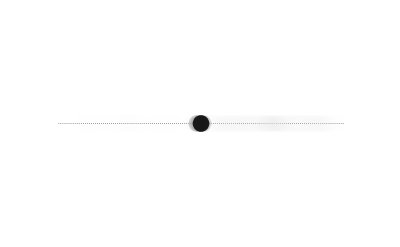

```mathematica
Show[
ListPlot[latticeRational,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {{-10,Max[Flatten[latticeRational]]+10},{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfuncBW[#[[3]],rng[[2]]],Point[#[[1;;2]]]
}&/@dataLDoSPBCSorted,
BaseStyle-> 18
]

]
```